SIRS Model

```mathematica
SS1 =NDSolve[{
x'[t] == - (0.3/(80*10^6))x[t]y[t] + 0.0167z[t], 
y'[t] ==(0.3/(80*10^6))x[t]y[t] - (1/16)y[t],
z'[t] == (1/16)y[t] - 0.0167z[t],  
x[0]== 80*10^6, y[0]== 1,  z[0]==0 }, {x,y,z},{t,0,200}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

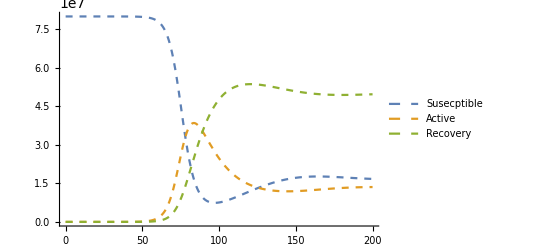

```mathematica
pp1 =Plot[{x[t]/.SS1,y[t]/.SS1,z[t]/.SS1},{t,0,200}, PlotRange->All,PlotStyle->Dashed,PlotLegends->{"Susecptible","Active", "Recovery"}]
```

Delayed SIRS Model

```mathematica
SS2= NDSolve[{
x'[t] == - (0.3/(80*10^6))x[t]y[t]+ 0.0167z[t],
y'[t] ==(0.3/(80*10^6))x[t]y[t] - (0.3/(80*10^6))x[t-14]y[t-14],
z'[t] == (0.3/(80*10^6))x[t-14]y[t-14]- 0.0167z[t],  
x[0]== 80*10^6,y[t/; t ≤0]== E^t,y[0]==150, z[0]== 0  }, {x,y,z},{t,0,200}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

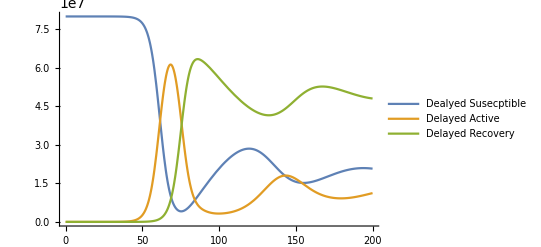

```mathematica
pp2 =Plot[{x[t]/.SS2,y[t]/.SS2,z[t]/.SS2},{t,0,200}, PlotRange->All,PlotLegends->{"Dealyed Susecptible"," Delayed Active", " Delayed Recovery"}]
```

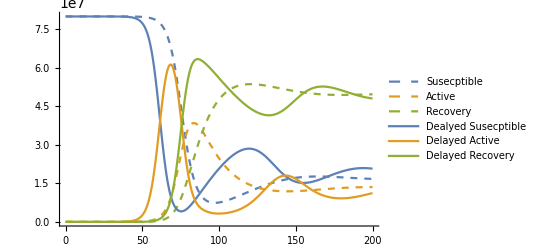

```mathematica
Show[pp1,pp2]
```

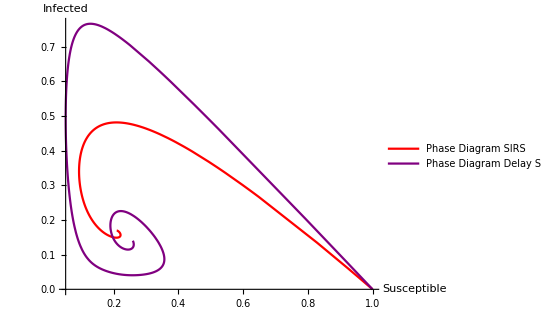

```mathematica
pp12 = ParametricPlot[Evaluate[{{x[t]/(80*10^6),y[t]/(80*10^6)}/.SS1, {x[t]/(80*10^6),y[t]/(80*10^6)}/.SS2}],{t,0,200}, PlotRange->All,PlotStyle->{Red, Purple},AxesLabel->{Susceptible, Infected},PlotLegends->{"Phase Diagram SIRS","Phase Diagram Delay SIRS"}]
```

Manipulating the Delay

```mathematica
Manipulate[Module[{SS33 = NDSolve[{
x'[t] == - (0.3/(80*10^6))x[t]y[t]+ 0.0167z[t],
y'[t] ==(0.3/(80*10^6))x[t]y[t] - (0.3/(80*10^6))x[t-u]y[t-u],
z'[t] == (0.3/(80*10^6))x[t-u]y[t-u]- 0.0167z[t],  
x[0]== 80*10^6,y[t/; t ≤0]== E^t,y[0]==150, z[0]== 0  }, {x,y,z},{t,0,200}]},Plot[{x[t]/.SS33,y[t]/.SS33,z[t]/.SS33},{t,0,200}, PlotRange->All, PlotLegends->{"Delay Susecptible"," Delay Active", " Delay Recovery"}]],{u,5,16}]
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

```mathematica
bp5 =Manipulate[Module[{SS34 = NDSolve[{
x'[t] == - (0.3/(80*10^6))x[t]y[t]+ 0.0167z[t],
y'[t] ==(0.3/(80*10^6))x[t]y[t] - (0.3/(80*10^6))x[t-u]y[t-u],
z'[t] == (0.3/(80*10^6))x[t-u]y[t-u]- 0.0167z[t],  
x[0]== 80*10^6,y[t/; t ≤0]== E^t,y[0]==150, z[0]== 0  }, {x,y,z},{t,0,200}]},ParametricPlot[Evaluate[{x[t]/(80*10^6),y[t]/(80*10^6)}/.SS34],{t,0,200},AxesLabel->{Susceptible, Infected}, PlotRange->All]],{u,5,16}]
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

Coupled Model

```mathematica
SS3 =NDSolve[
{x1'[t] == - x1[t]((0.3/(80*10^6))y1[t] + (0.5/(80*10^6))y2[t]),
x2'[t] == - x2[t]((0.3/(80*10^6))y1[t] + (0.5/(50*10^6))y2[t]), 
y1'[t] ==x1[t]((0.3/(80*10^6))y1[t] + (0.5/(80*10^6))y2[t]) - (1/16)y1[t],
y2'[t] ==x2[t]((0.3/(50*10^6))y1[t] + (0.5/(50*10^6))y2[t]) - (1/10)y2[t],
z1'[t] == (1/16)y1[t],
z2'[t] == (1/10)y2[t],  
x1[0]== 80*10^6, y1[0]== 150,  z1[0]==0,x2[0]== 50*10^6, y2[0]== 100,  z2[0]==0  }, {x1,y1,z1,x2,y2,z2},{t,0,200}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…],x2→InterpolatingFunction[…],y2→InterpolatingFunction[…],z2→InterpolatingFunction[…]}}

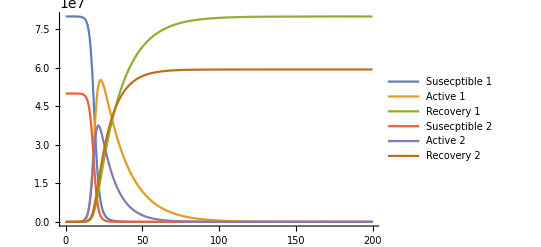

```mathematica
pp3 =Plot[{x1[t]/.SS3,y1[t]/.SS3,z1[t]/.SS3,x2[t]/.SS3,y2[t]/.SS3,z2[t]/.SS3},{t,0,200}, PlotRange->All,PlotLegends->{"Susecptible 1","Active 1", "Recovery 1","Susecptible 2","Active 2", "Recovery 2"}]
```

Delayed Coupling

```mathematica
SS4 =NDSolve[
{x1'[t] == - x1[t]((0.3/(80*10^6))y1[t] + (0.5/(80*10^6))y2[t]),
x2'[t] == - x2[t]((0.3/(50*10^6))y1[t] + (0.5/(50*10^6))y2[t]), 
y1'[t]==x1[t] ((0.3/(80*10^6)) y1[t]+0.5/(80*10^6) y2[t])-x1[t-14] ((0.3/(80*10^6)) y1[t-14]+(0.5/(80*10^6)) y2[t-14]),
y2'[t]==x2[t] ((0.3/(50*10^6)) y1[t]+(0.5/(50*10^6)) y2[t])-x2[t-14] ((0.3/(50*10^6)) y1[t-14]+(0.5/(50*10^6)) y2[t-14]),
z1'[t]==x1[t-14] ((0.3/(80*10^6)) y1[t-14]+(0.5/(80*10^6)) y2[t-14]),
z2'[t]==x2[t-14] ((0.3/(50*10^6)) y1[t-14]+(0.5/(50*10^6)) y2[t-14]),
x1[0]== 80*10^6, y1[0]== 150, y1[t/; t ≤0]== E^t, z1[0]==0,x2[0]== 50*10^6,y2[t/; t ≤0]== E^t, y2[0]== 100,  z2[0]==0  }, {x1,y1,z1,x2,y2,z2},{t,0,200}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…],x2→InterpolatingFunction[…],y2→InterpolatingFunction[…],z2→InterpolatingFunction[…]}}

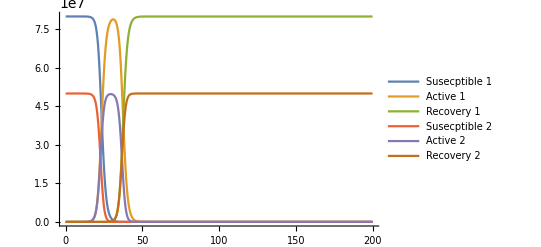

```mathematica
pp4 =Plot[{x1[t]/.SS4,y1[t]/.SS4,z1[t]/.SS4,x2[t]/.SS4,y2[t]/.SS4,z2[t]/.SS4},{t,0,200}, PlotRange->All,PlotLegends->{"Susecptible 1","Active 1", "Recovery 1","Susecptible 2","Active 2", "Recovery 2"}]
```

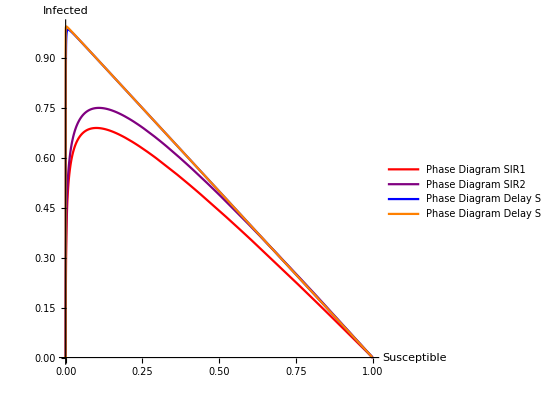

```mathematica
pp13 = ParametricPlot[Evaluate[{{x1[t]/(80*10^6),y1[t]/(80*10^6)}/.SS3,{x2[t]/(50*10^6),y2[t]/(50*10^6)}/.SS3, {x1[t]/(80*10^6),y1[t]/(80*10^6)}/.SS4,{x2[t]/(50*10^6),y2[t]/(50*10^6)}/.SS4}],{t,0,200}, PlotRange->All,PlotStyle->{Red, Purple,Blue,Orange},AxesLabel->{Susceptible, Infected},PlotLegends->{"Phase Diagram SIR1","Phase Diagram SIR2","Phase Diagram Delay SIR1","Phase Diagram Delay SIR2"}]
```

Different Delay

```mathematica
SS5 =NDSolve[
{x1'[t] == - x1[t]((0.3/(80*10^6))y1[t] + (0.5/(80*10^6))y2[t]),
x2'[t] == - x2[t]((0.3/(50*10^6))y1[t] + (0.5/(50*10^6))y2[t]), 
y1'[t]==x1[t] ((0.3/(80*10^6)) y1[t]+(0.5/(80*10^6)) y2[t])-x1[t-14] (0.3/(80*10^6)) y1[t-14]-x1[t-10] (0.5/(80*10^6)) y2[t-10],
y2'[t]==x2[t] ((0.3/(50*10^6)) y1[t]+(0.5/(50*10^6)) y2[t])-x2[t-14] (0.3/(50*10^6)) y1[t-14]-x2[t-10](0.5/(50*10^6)) y2[t-10],
z1'[t]==x1[t-14] (0.3/(80*10^6)) y1[t-14]+x1[t-10] (0.5/(80*10^6)) y2[t-10],
z2'[t]==x2[t-14] (0.3/(50*10^6)) y1[t-14]+x2[t-10](0.5/(50*10^6)) y2[t-10],
x1[0]== 80*10^6, y1[0]== 150, y1[t/; t ≤0]== E^t, z1[0]==0,x2[0]== 50*10^6,y2[t/; t ≤0]== E^t, y2[0]== 100,  z2[0]==0  }, {x1,y1,z1,x2,y2,z2},{t,0,200}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…],x2→InterpolatingFunction[…],y2→InterpolatingFunction[…],z2→InterpolatingFunction[…]}}

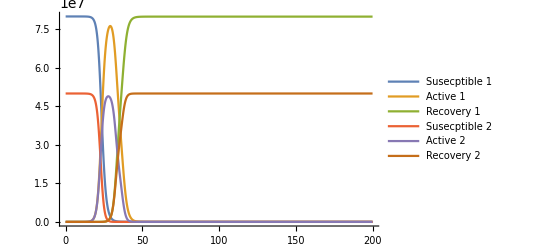

```mathematica
pp5 = Plot[{x1[t]/.SS5,y1[t]/.SS5,z1[t]/.SS5,x2[t]/.SS5,y2[t]/.SS5,z2[t]/.SS5},{t,0,200}, PlotRange->All,PlotLegends->{"Susecptible 1","Active 1", "Recovery 1","Susecptible 2","Active 2", "Recovery 2"}]
```

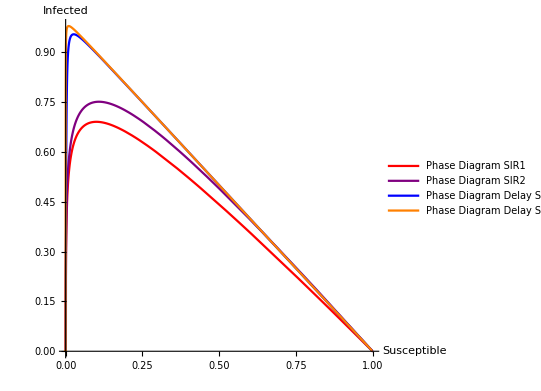

```mathematica
pp13 = ParametricPlot[Evaluate[{{x1[t]/(80*10^6),y1[t]/(80*10^6)}/.SS3,{x2[t]/(50*10^6),y2[t]/(50*10^6)}/.SS3, {x1[t]/(80*10^6),y1[t]/(80*10^6)}/.SS5,{x2[t]/(50*10^6),y2[t]/(50*10^6)}/.SS5}],{t,0,200}, PlotRange->All,PlotStyle->{Red, Purple,Blue,Orange},AxesLabel->{Susceptible, Infected},PlotLegends->{"Phase Diagram SIR1","Phase Diagram SIR2","Phase Diagram Delay SIR1","Phase Diagram Delay SIR2"}]
```

Combined model (Sirs and coupled with diff delay)

```mathematica
SS6 =NDSolve[
{x1'[t] == - x1[t]((0.3/(80*10^6))y1[t] + (0.5/(80*10^6))y2[t])+ 0.0167z1[t],
x2'[t] == - x2[t]((0.3/(50*10^6))y1[t] + (0.5/(50*10^6))y2[t])+ 0.02z2[t], 
y1'[t]==x1[t] ((0.3/(80*10^6)) y1[t]+(0.5/(80*10^6)) y2[t])-x1[t-14] (0.3/(80*10^6)) y1[t-14]-x1[t-10] (0.5/(80*10^6)) y2[t-10],
y2'[t]==x2[t] ((0.3/(50*10^6)) y1[t]+(0.5/(50*10^6)) y2[t])-x2[t-14] (0.3/(50*10^6)) y1[t-14]-x2[t-10](0.5/(50*10^6)) y2[t-10],
z1'[t]==x1[t-14] (0.3/(80*10^6)) y1[t-14]+x1[t-10] (0.5/(80*10^6)) y2[t-10]- 0.0167z1[t],
z2'[t]==x2[t-14] (0.3/(50*10^6)) y1[t-14]+x2[t-10](0.5/(50*10^6)) y2[t-10]- 0.02z2[t],
x1[0]== 80*10^6, y1[0]== 150, y1[t/; t ≤0]== E^t, z1[0]==0,x2[0]== 50*10^6,y2[t/; t ≤0]== E^t, y2[0]== 100,  z2[0]==0  }, {x1,y1,z1,x2,y2,z2},{t,0,200}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…],x2→InterpolatingFunction[…],y2→InterpolatingFunction[…],z2→InterpolatingFunction[…]}}

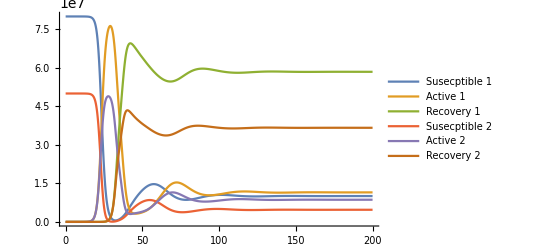

```mathematica
pp6 = Plot[{x1[t]/.SS6,y1[t]/.SS6,z1[t]/.SS6,x2[t]/.SS6,y2[t]/.SS6,z2[t]/.SS6},{t,0,200}, PlotRange->All,PlotLegends->{"Susecptible 1","Active 1", "Recovery 1","Susecptible 2","Active 2", "Recovery 2"}]
```

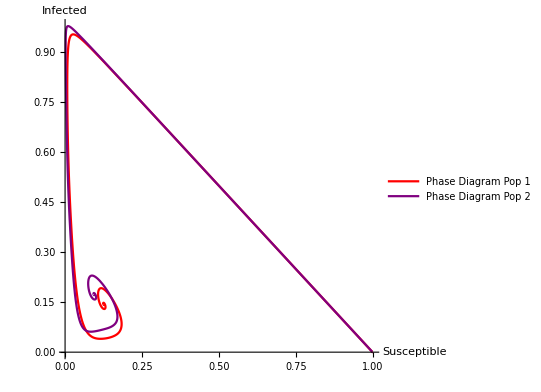

```mathematica
pp14 = ParametricPlot[Evaluate[{{x1[t]/(80*10^6),y1[t]/(80*10^6)}/.SS6,{x2[t]/(50*10^6),y2[t]/(50*10^6)}/.SS6}],{t,0,200}, PlotRange->All,PlotStyle->{Red, Purple,Blue,Orange},AxesLabel->{Susceptible, Infected},PlotLegends->{"Phase Diagram Pop 1","Phase Diagram Pop 2"}]
```

Two Strain model

```mathematica
S2= NDSolve[{
x'[t] == - (0.3/(80*10^6))x[t]y1[t] -(0.5/(80*10^6))x[t]y2[t] ,
y1'[t] ==(0.3/(80*10^6))x[t]y1[t] - (0.3/(80*10^6))x[t-14]y1[t-14],
y2'[t] ==(0.5/(80*10^6))x[t]y2[t] - (0.5/(80*10^6))x[t-20]y2[t-20],
z'[t] == (0.3/(80*10^6))x[t-14]y1[t-14]+ (0.5/(80*10^6))x[t-20]y2[t-20], 
x[0]== 80*10^6,y1[t/; t ≤0]== E^t,y1[0]==150,y2[t/; t ≤0]== E^t,y2[0]==350, z[0]== 0 }, {x,y1,y2,z},{t,0,200}]
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{{x→InterpolatingFunction[…],y1→InterpolatingFunction[…],y2→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

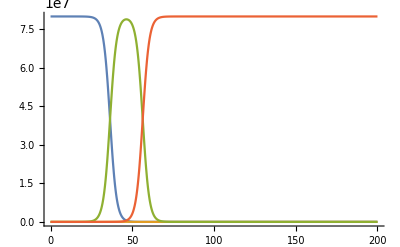

```mathematica
p2 = Plot[{x[t]/.S2,y1[t]/.S2,y2[t]/.S2,z[t]/.S2},{t,0,200}, PlotRange->All]
```

Lockdown Delay SIR

```mathematica
Manipulate[Module[{AS5 = NDSolve[{x'[t] == - ((1-l)(0.3/(80*10^6)))x[t]y[t], 
y'[t] ==((1-l)(0.3/(80*10^6)))x[t]y[t] - ((1-l)(0.3/(80*10^6)))x[t-u]y[t-u],
z'[t] == ((1-l)(0.3/(80*10^6)))x[t-u]y[t-u],  
x[0]== 80*10^6,y[t/; t ≤0]== E^t,y[0]==150, z[0]== 0  }, {x,y,z},{t,0,200}]},Plot[{x[t]/.AS5,y[t]/.AS5,z[t]/.AS5},{t,0,200}, PlotRange->All, PlotLegends->{"Delay Susecptible"," Delay Active", " Delay Recovery"}]],{u,5,16},{l,0,1}]
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

```mathematica
Manipulate[Module[{AS6 = NDSolve[{x'[t] == - ((1-l)(0.3/(80*10^6)))x[t]y[t] + (r)z[t], 
y'[t] ==((1-l)(0.3/(80*10^6)))x[t]y[t] - ((1-l)(0.3/(80*10^6)))x[t-u]y[t-u],
z'[t] == ((1-l)(0.3/(80*10^6)))x[t-u]y[t-u]-(r)z[t],  
x[0]== 80*10^6,y[t/; t ≤0]== E^t,y[0]==150, z[0]== 0  }, {x,y,z},{t,0,200}]},Plot[{x[t]/.AS6,y[t]/.AS6,z[t]/.AS6},{t,0,200}, PlotRange->All, PlotLegends->{"Delay Susecptible"," Delay Active", " Delay Recovery"}]],{u,5,16},{l,0,1},{r,0.03,0.3}]
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

```mathematica
Manipulate[Module[{AS7 = NDSolve[{x'[t] == - ((1-l)(0.3/(80*10^6)))x[t]y[t] + (r)z[t], 
y'[t] ==((1-l)(0.3/(80*10^6)))x[t]y[t] - ((1-l)(0.3/(80*10^6)))x[t-u]y[t-u],
z'[t] == ((1-l)(0.3/(80*10^6)))x[t-u]y[t-u]-(r)z[t],  
x[0]== 80*10^6,y[t/; t ≤0]== E^t,y[0]==150, z[0]== 0  }, {x,y,z},{t,0,200}]},Plot[{x[t]/.AS7,y[t]/.AS7,z[t]/.AS7},{t,0,200}, PlotRange->All, PlotLegends->{"Delay Susecptible"," Delay Active", " Delay Recovery"}]],{u,5,16},{l,0,1},{r,0.03,0.3}]
```

Coupled SIRS without Delay

```mathematica
AS1 =NDSolve[
{x1'[t] == - x1[t]((0.3/(80*10^6))y1[t] + (0.5/(80*10^6))y2[t]) + 0.0167z1[t],
x2'[t] == - x2[t]((0.3/(50*10^6))y1[t] + (0.5/(50*10^6))y2[t])+ 0.02z2[t], 
y1'[t] ==x1[t]((0.3/(80*10^6))y1[t] + (0.5/(80*10^6))y2[t]) - (1/16)y1[t],
y2'[t] ==x2[t]((0.3/(50*10^6))y1[t] + (0.5/(50*10^6))y2[t]) - (1/10)y2[t],
z1'[t] == (1/16)y1[t]-0.0167z1[t],
z2'[t] == (1/10)y2[t] - 0.02z2[t],  
x1[0]== 80*10^6, y1[0]== 150,  z1[0]==0,x2[0]== 50*10^6, y2[0]== 100,  z2[0]==0  }, {x1,y1,z1,x2,y2,z2},{t,0,200}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…],x2→InterpolatingFunction[…],y2→InterpolatingFunction[…],z2→InterpolatingFunction[…]}}

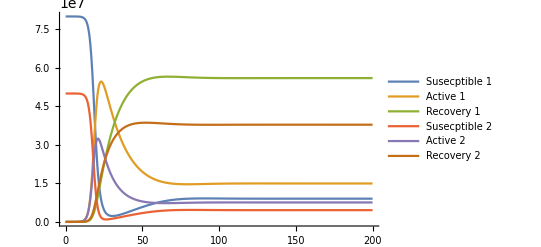

```mathematica
ap1 = Plot[{x1[t]/.AS1,y1[t]/.AS1,z1[t]/.AS1,x2[t]/.AS1,y2[t]/.AS1,z2[t]/.AS1},{t,0,200}, PlotRange->All,PlotLegends->{"Susecptible 1","Active 1", "Recovery 1","Susecptible 2","Active 2", "Recovery 2"}]
```

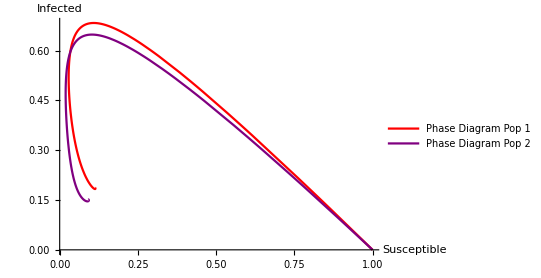

```mathematica
ap14 = ParametricPlot[Evaluate[{{x1[t]/(80*10^6),y1[t]/(80*10^6)}/.AS1,{x2[t]/(50*10^6),y2[t]/(50*10^6)}/.AS1}],{t,0,200}, PlotRange->All,PlotStyle->{Red, Purple,Blue,Orange},AxesLabel->{Susceptible, Infected},PlotLegends->{"Phase Diagram Pop 1","Phase Diagram Pop 2"}]
```